# Supplementary tensors

## ITensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<ITensor`
<<DummyArray`
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.041338,Null}

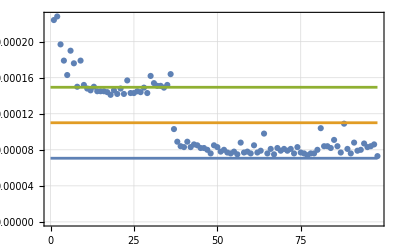

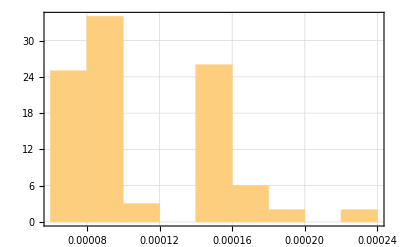

{0.0000706484,0.000110031,0.000149413}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[2]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.043548,Null}

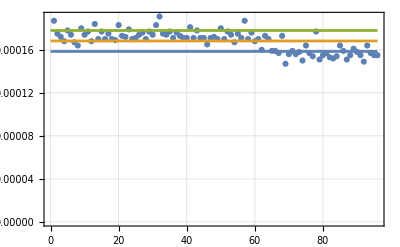

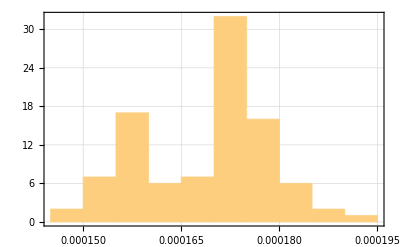

{0.000158487,0.000168219,0.00017795}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[3]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.107719,Null}

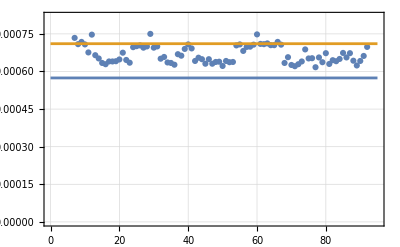

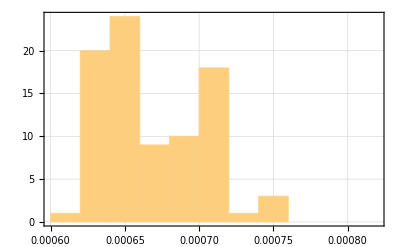

{0.00057425,0.000710863,0.000847476}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[4]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.627652,Null}

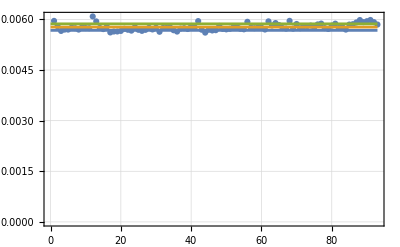

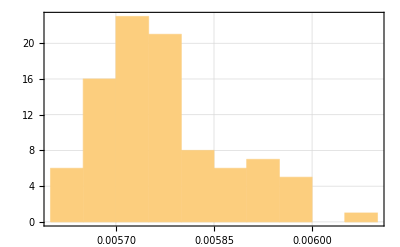

{0.00567589,0.00577231,0.00586873}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[5]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{7.81731,Null}

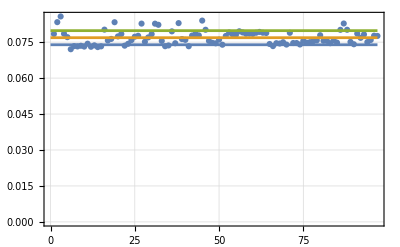

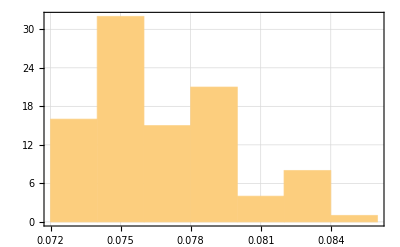

{0.0739117,0.0768531,0.0797944}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<ITensor`;
	AppendTo[theData,Timing[ITensor[DummyArray[6]]][[1]]];
	Clear[ITensor];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## CTensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.359795,Null}

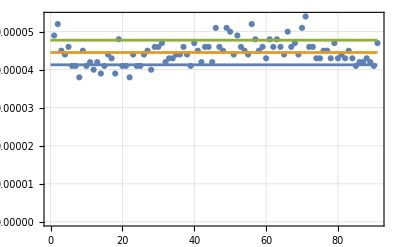

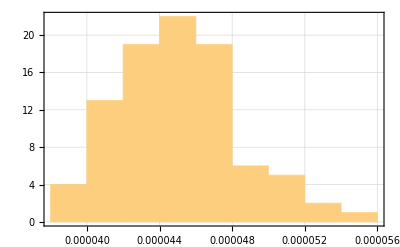

{0.0000412911,0.0000445275,0.0000477639}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.076468,Null}

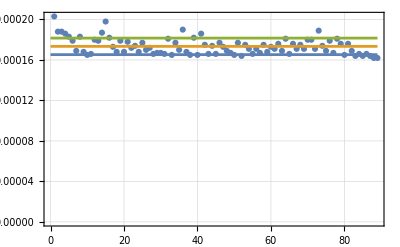

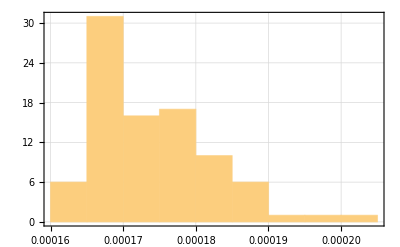

{0.000165282,0.000173449,0.000181617}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.184159,Null}

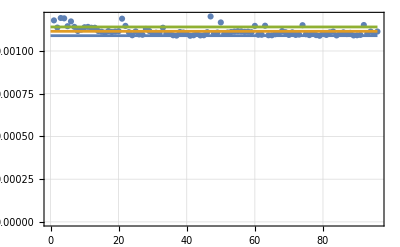

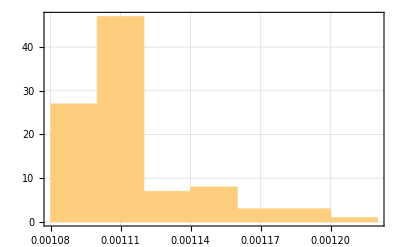

{0.00108959,0.00111509,0.00114059}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1.28031,Null}

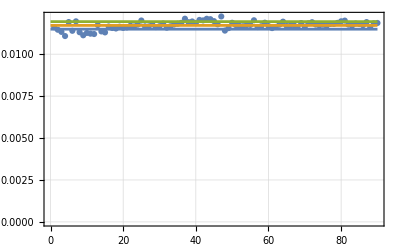

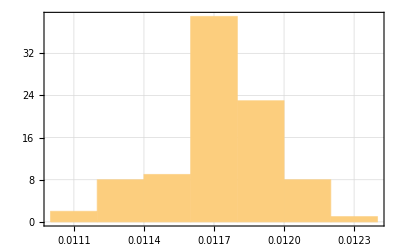

{0.0114897,0.0117147,0.0119397}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{16.4981,Null}

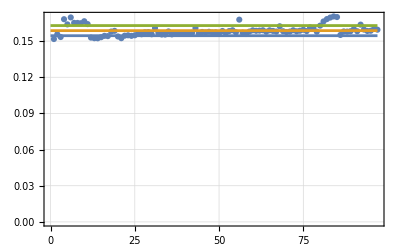

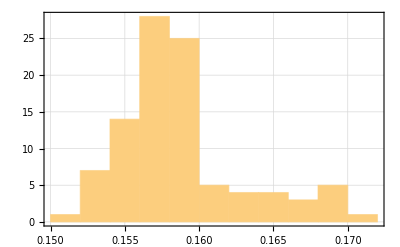

{0.15448,0.158682,0.162885}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{282.524,Null}

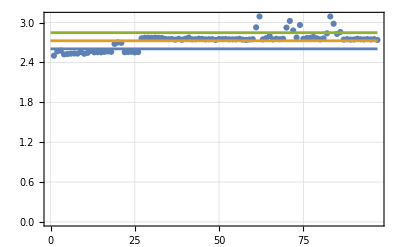

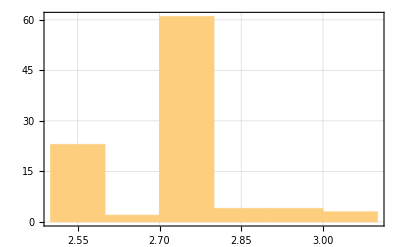

{2.60437,2.72585,2.84733}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[6]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C1Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.067722,Null}

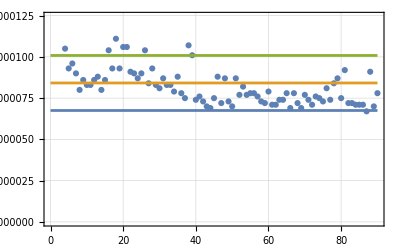

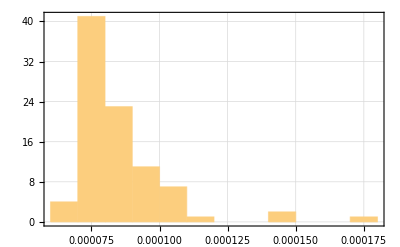

{0.000067515,0.0000841889,0.000100863}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.095126,Null}

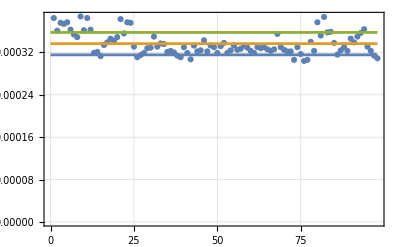

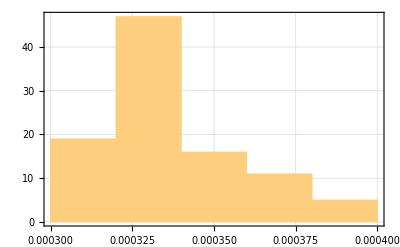

{0.000315476,0.000336653,0.00035783}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.315107,Null}

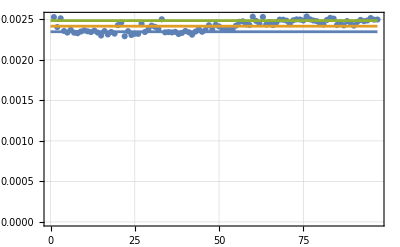

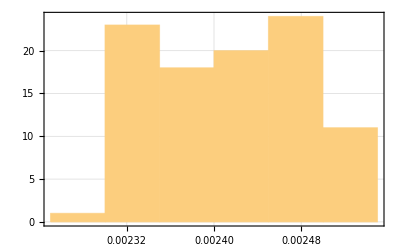

{0.0023473,0.00241598,0.00248466}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{2.60451,Null}

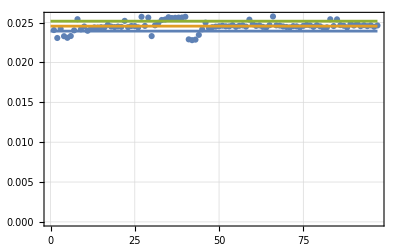

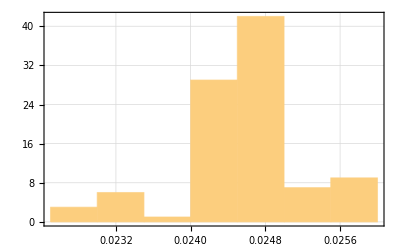

{0.0239279,0.0245514,0.0251749}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{36.3925,Null}

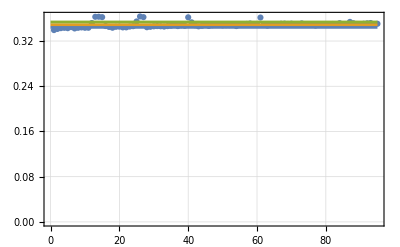

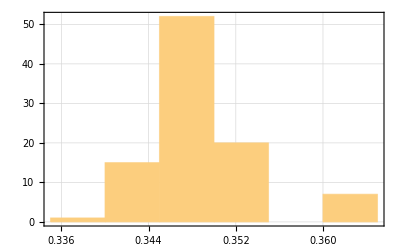

{0.344172,0.348938,0.353705}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{627.948,Null}

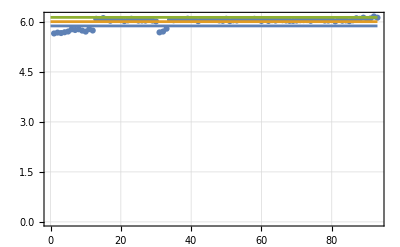

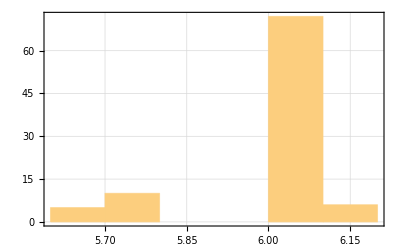

{5.88015,6.0086,6.13704}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[6]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0},PlotTheme->"Detailed"],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData,PlotTheme->"Detailed"]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

## C2Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.06664,Null}

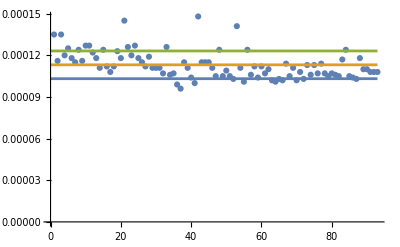

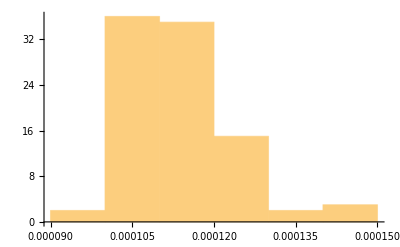

{0.000103169,0.000113161,0.000123154}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.111898,Null}

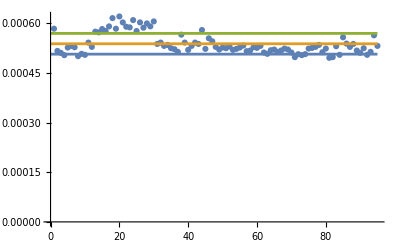

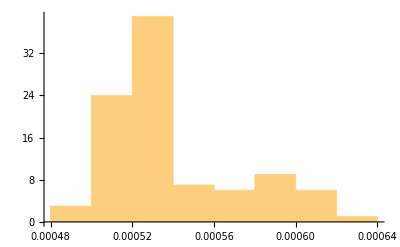

{0.00050707,0.000538411,0.000569751}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.490602,Null}

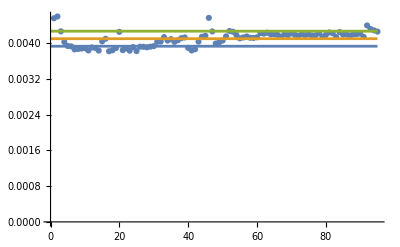

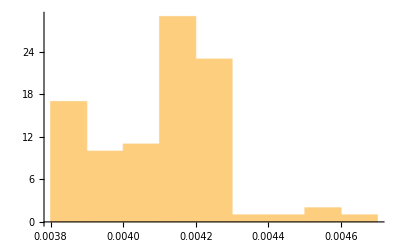

{0.00393606,0.00410457,0.00427307}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{4.67363,Null}

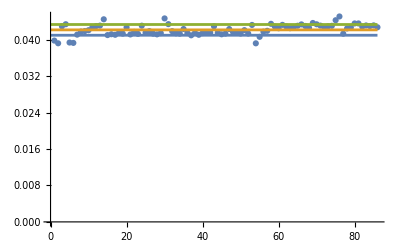

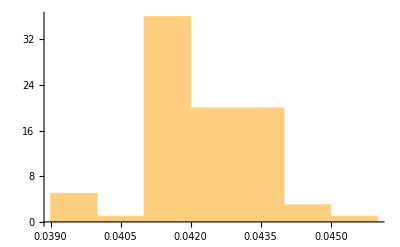

{0.0410159,0.0421965,0.0433772}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{61.4766,Null}

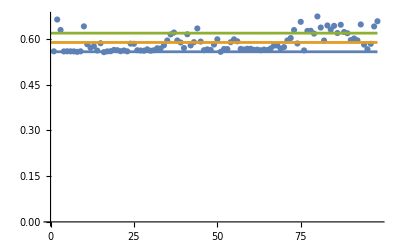

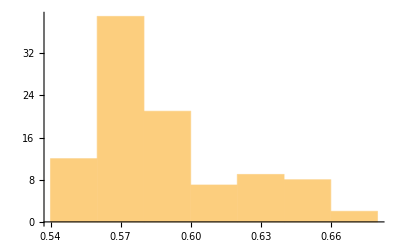

{0.558233,0.588774,0.619315}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[6]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C3Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.069477,Null}

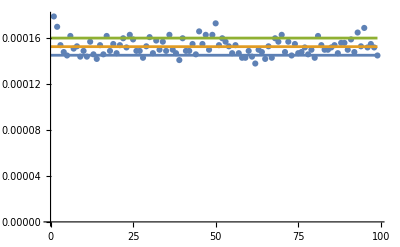

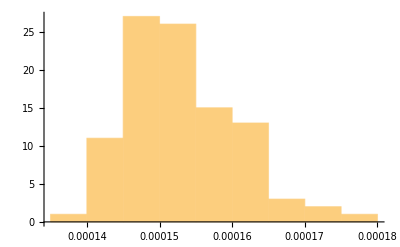

{0.000145211,0.000152687,0.000160163}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.135533,Null}

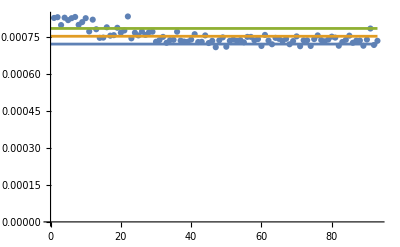

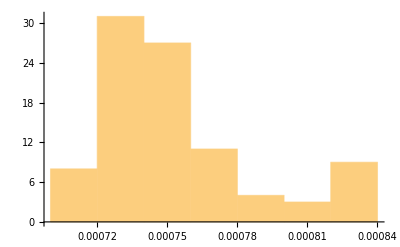

{0.000722763,0.000754516,0.000786269}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.68708,Null}

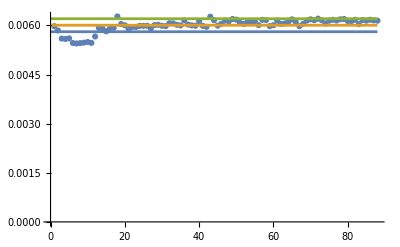

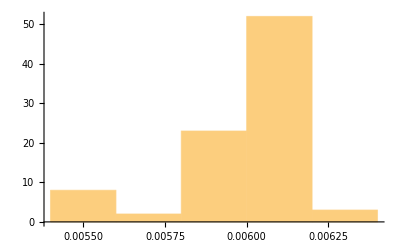

{0.00580594,0.00600425,0.00620256}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{6.549,Null}

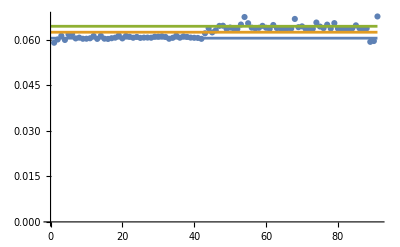

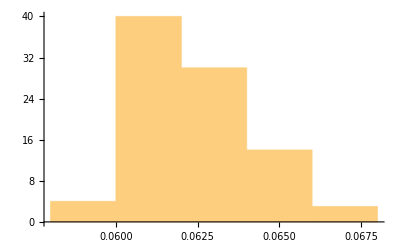

{0.0605066,0.0624662,0.0644257}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{89.0066,Null}

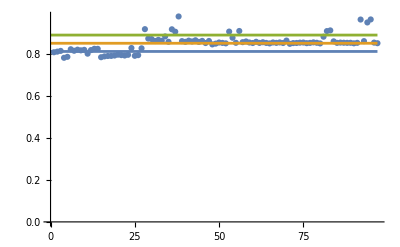

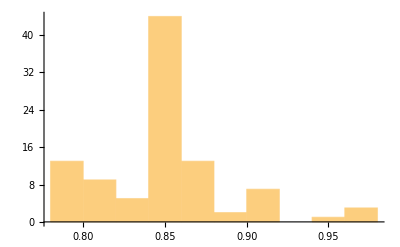

{0.811144,0.850163,0.889182}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[6]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## C4Tensor

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.102365,Null}

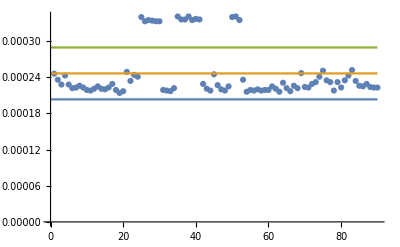

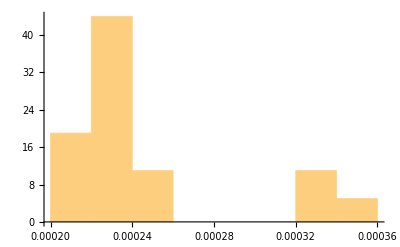

{0.00020338,0.000246444,0.000289509}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[1]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.204927,Null}

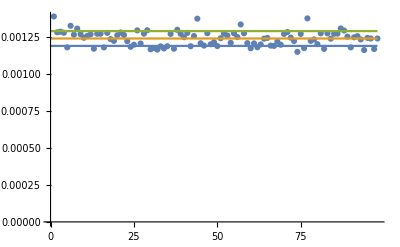

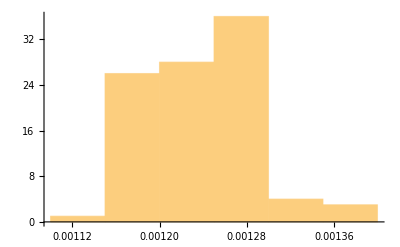

{0.00118901,0.00123905,0.00128909}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[2]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1.0987,Null}

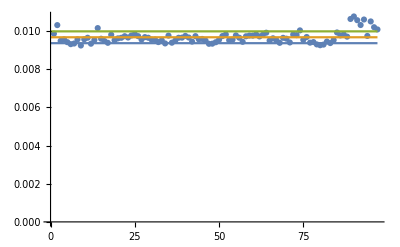

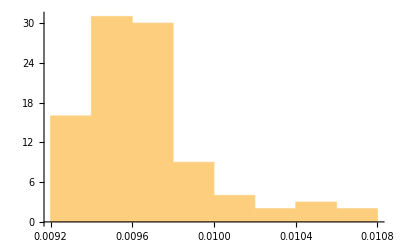

{0.00935873,0.00966827,0.00997781}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{10.5664,Null}

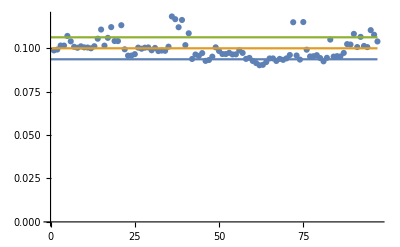

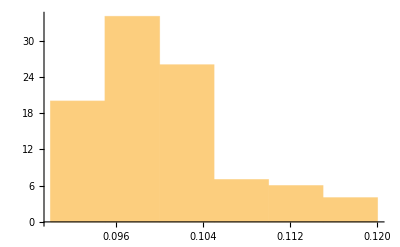

{0.0936306,0.0999565,0.106283}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[4]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{131.925,Null}

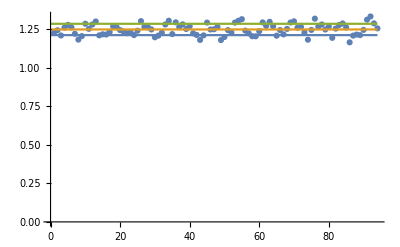

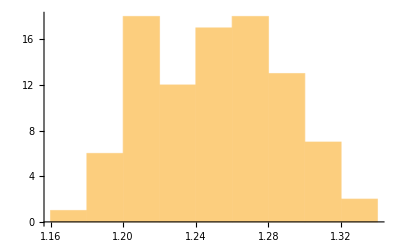

{1.21316,1.24995,1.28674}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[5]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[]
```

## CTensors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<CTensorGeneral`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.210531,Null}

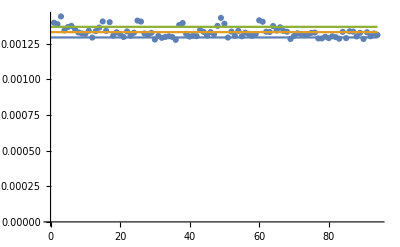

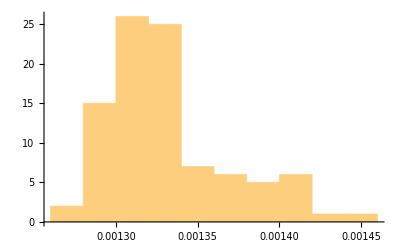

{0.00129371,0.00133096,0.0013682}

```mathematica
theData1 = {};
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{0.357652,Null}

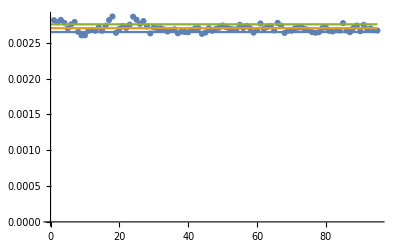

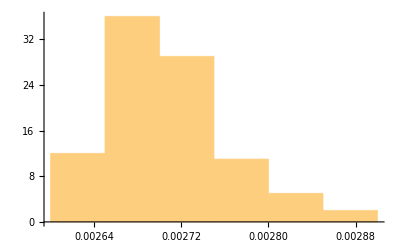

{0.00265104,0.00270518,0.00275932}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{0.543922,Null}

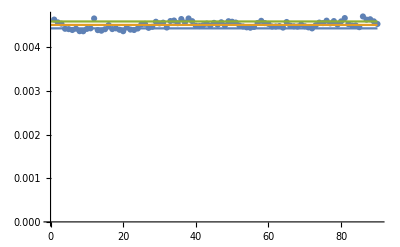

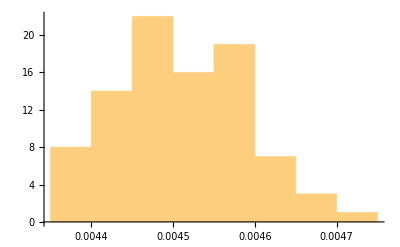

{0.00443133,0.00451036,0.00458938}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{0.746075,Null}

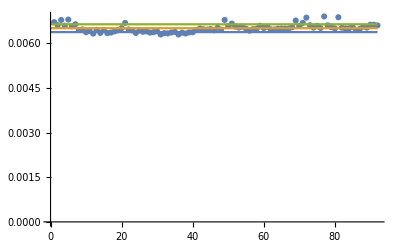

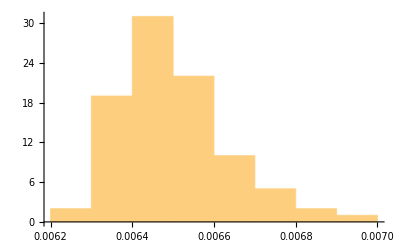

{0.00637449,0.00650574,0.00663699}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{1.10163,Null}

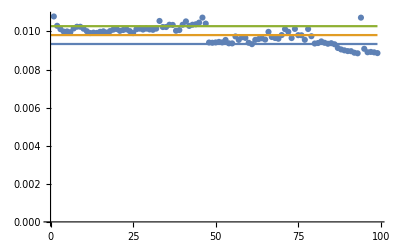

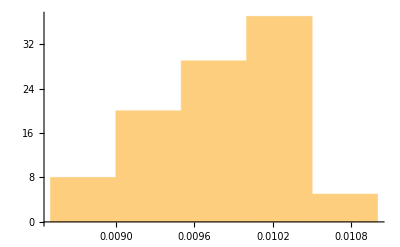

{0.00933952,0.00980725,0.010275}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

{1.31916,Null}

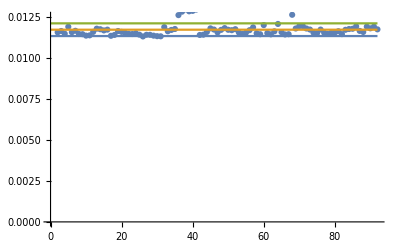

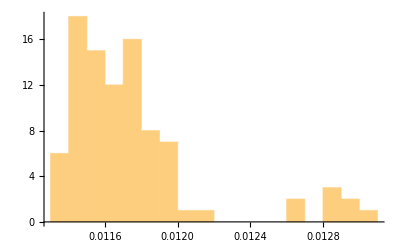

{0.0113602,0.0117485,0.0121368}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<CTensorGeneral`;
	AppendTo[theData,Timing[CTensorGeneral[{μ1,ν1,μ2,ν2,μ3,ν3,μ4,ν4,μ5,ν5},DummyArray[3]]][[1]]];
	Clear[CTensorGeneral];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
AppendTo[theData1,Mean[theData]];
```

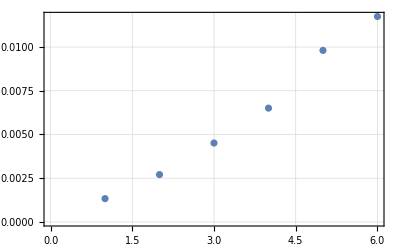

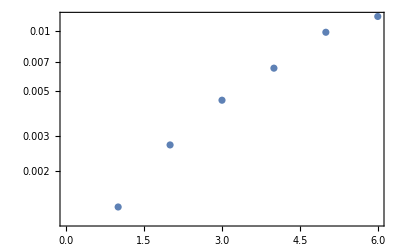

```mathematica
ListPlot[theData1,PlotTheme->"Detailed"]
ListLogPlot[theData1,PlotTheme->"Detailed"]
```

```mathematica
NotebookSave[]
```

# Scalar-graviton vertices

## Kinetic term

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
<<DummyArray`
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{0.552584,Null}

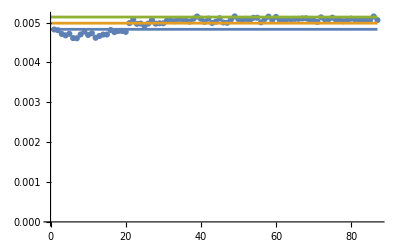

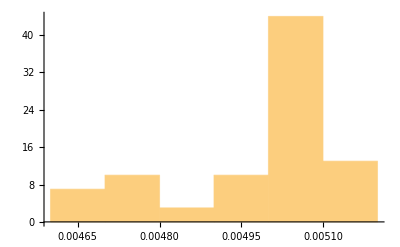

{0.00483142,0.00498544,0.00513946}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[1],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1.94713,Null}

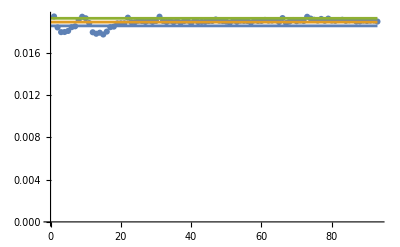

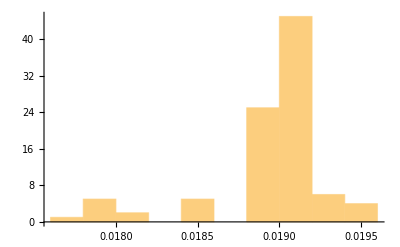

{0.0185654,0.0189238,0.0192821}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[2],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{37.7014,Null}

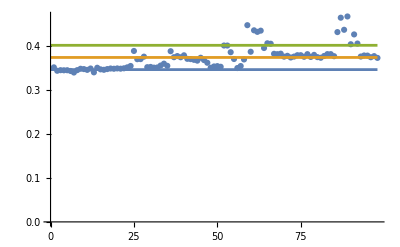

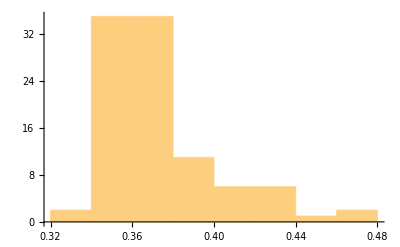

{0.346066,0.373675,0.401284}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarVertex[DummyArray[3],p1,p2,m]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Potential term

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonScalarVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.049902,Null}

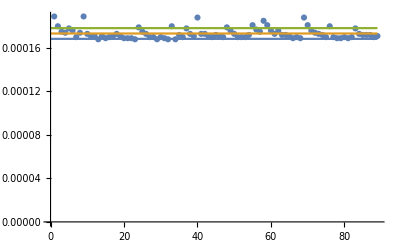

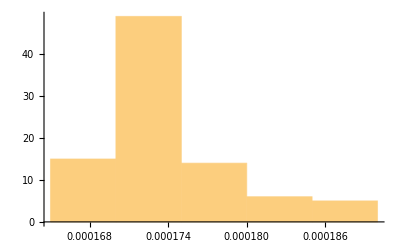

{0.000168388,0.000173326,0.000178264}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarPotentialVertex[DummyArray[1],λ]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarPotentialVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.067227,Null}

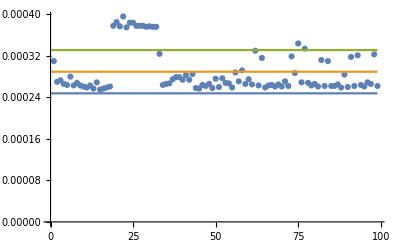

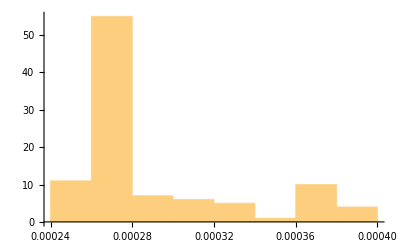

{0.000247816,0.000289525,0.000331234}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarPotentialVertex[DummyArray[2],λ]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarPotentialVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{0.102959,Null}

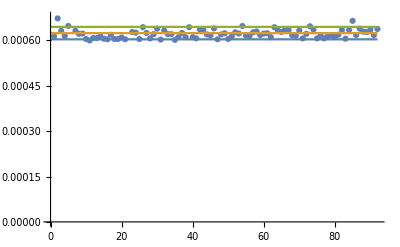

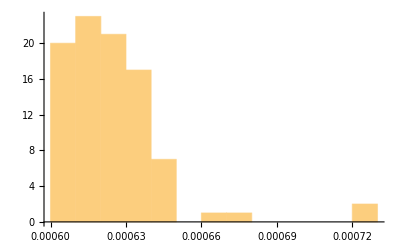

{0.000603838,0.000624467,0.000645097}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonScalarVertex`;
	AppendTo[theData,Timing[GravitonScalarPotentialVertex[DummyArray[3],λ]][[1]]];
	Clear[GravitonScalarVertex`GravitonScalarPotentialVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

# Graviton-fermion vertex

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonFermionVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.535343,Null}

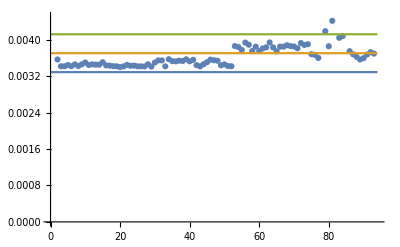

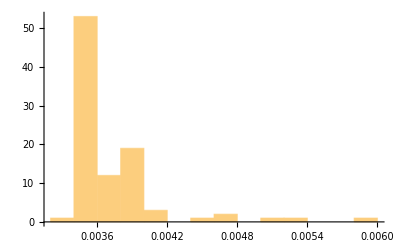

{0.00328597,0.0037013,0.00411663}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonFermionVertex`;
	AppendTo[theData,Timing[GravitonFermionVertex[DummyArray[1],p1,p2,m]][[1]]];
	Clear[GravitonFermionVertex`GravitonFermionVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{2.09279,Null}

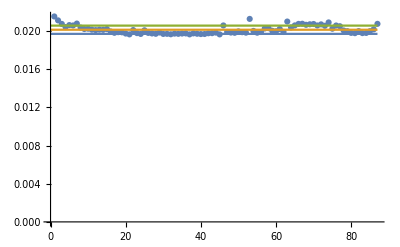

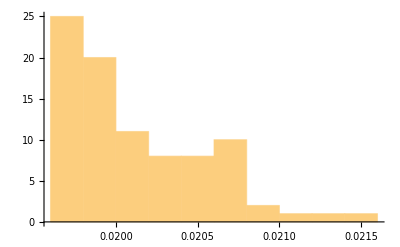

{0.0196973,0.0201302,0.020563}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonFermionVertex`;
	AppendTo[theData,Timing[GravitonFermionVertex[DummyArray[2],p1,p2,m]][[1]]];
	Clear[GravitonFermionVertex`GravitonFermionVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{21.271,Null}

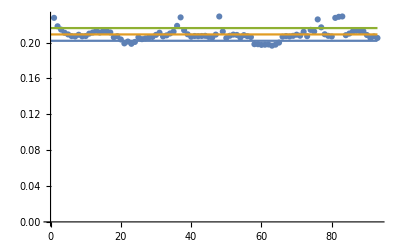

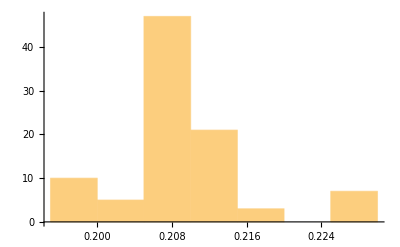

{0.202011,0.209103,0.216194}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonFermionVertex`;
	AppendTo[theData,Timing[GravitonFermionVertex[DummyArray[3],p1,p2,m]][[1]]];
	Clear[GravitonFermionVertex`GravitonFermionVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

# Graviton-vector vertices

## Massive vectors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{2.69415,Null}

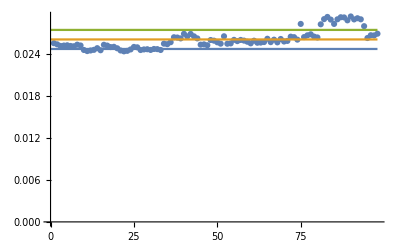

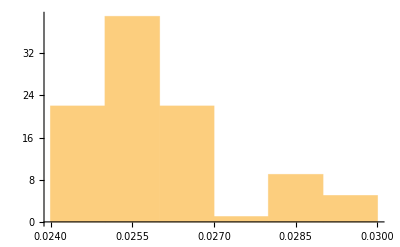

{0.0246659,0.026025,0.0273842}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonMassiveVectorVertex[DummyArray[1],λ1,p1,λ2,p2,m]][[1]]];
	Clear[GravitonVectorVertex`GravitonMassiveVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{25.1066,Null}

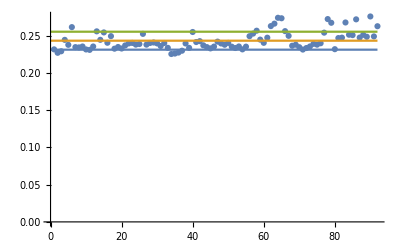

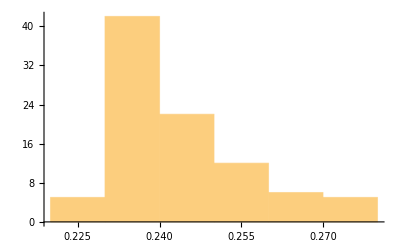

{0.231465,0.24354,0.255615}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonMassiveVectorVertex[DummyArray[2],λ1,p1,λ2,p2,m]][[1]]];
	Clear[GravitonVectorVertex`GravitonMassiveVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{335.327,Null}

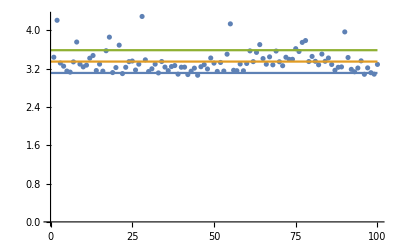

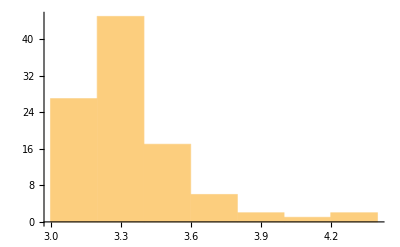

{3.11245,3.3504,3.58834}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonMassiveVectorVertex[DummyArray[3],λ1,p1,λ2,p2,m]][[1]]];
	Clear[GravitonVectorVertex`GravitonMassiveVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Massless vectors

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{4.546,Null}

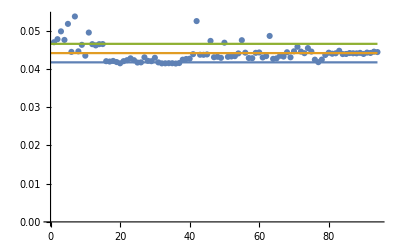

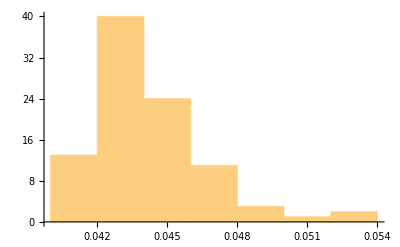

{0.0417258,0.0441453,0.0465648}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorVertex[DummyArrayK[1],λ1,p1,λ2,p2,ε]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{62.441,Null}

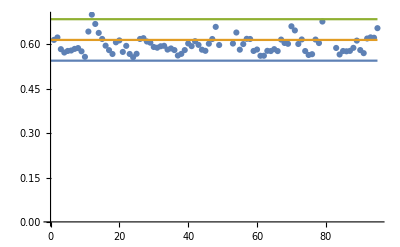

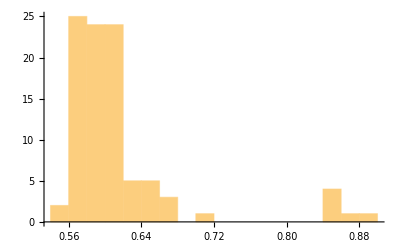

{0.545026,0.615131,0.685237}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorVertex[DummyArrayK[2],λ1,p1,λ2,p2,ε]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorVertex[DummyArrayK[3],λ1,p1,λ2,p2,ε]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Ghosts

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVectorVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{0.362873,Null}

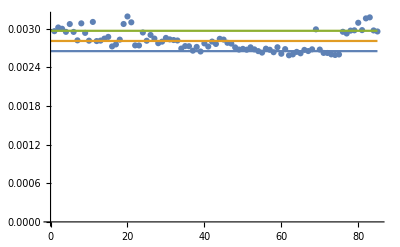

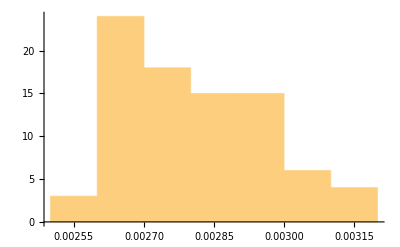

{0.00265066,0.00280848,0.00296631}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorGhostVertex[DummyArray[1],p1,p2]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorGhostVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1.88871,Null}

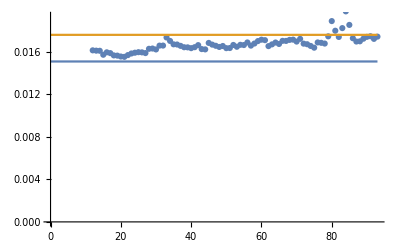

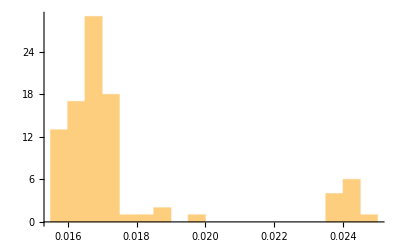

{0.0150827,0.0175866,0.0200905}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorGhostVertex[DummyArray[2],p1,p2]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorGhostVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{17.4075,Null}

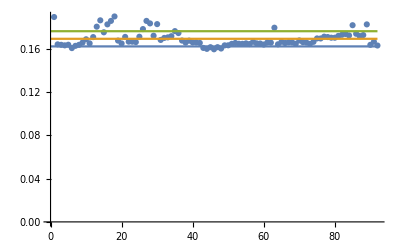

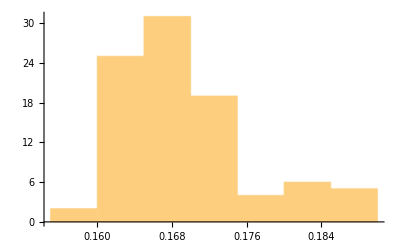

{0.162189,0.16921,0.176231}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVectorVertex`;
	AppendTo[theData,Timing[GravitonVectorGhostVertex[DummyArray[3],p1,p2]][[1]]];
	Clear[GravitonVectorVertex`GravitonVectorGhostVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

# Graviton vertices

## Pure graviton vertices

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
<<DummyArray`
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

{11.9825,Null}

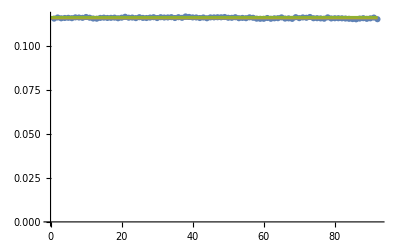

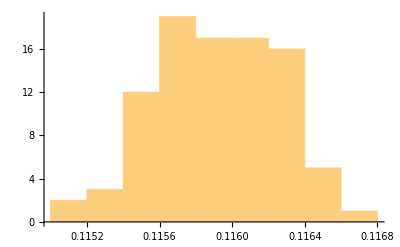

{0.115586,0.115924,0.116261}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonVertex[DummyArrayK[2]]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{505.407,Null}

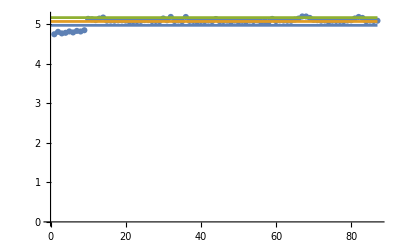

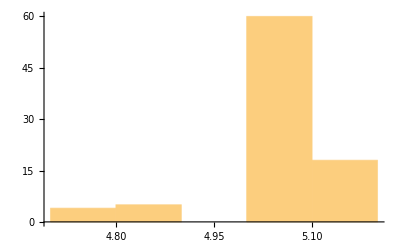

{4.96529,5.06259,5.1599}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonVertex[DummyArrayK[3]]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```

## Graviton-ghost vertex

```mathematica
SetDirectory[NotebookDirectory[]];
SetDirectory["../Rules"];
<<GravitonVertex`
<<DummyArray`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

{4.83899,Null}

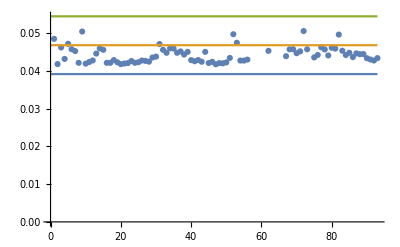

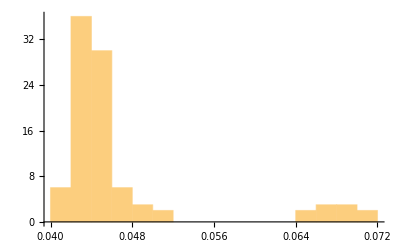

{0.0391109,0.0467495,0.0543881}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonGhostVertex[DummyArrayK[1],μ,p1,ν,p2]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{99.2485,Null}

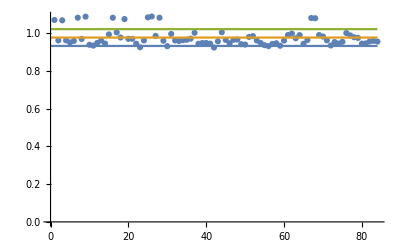

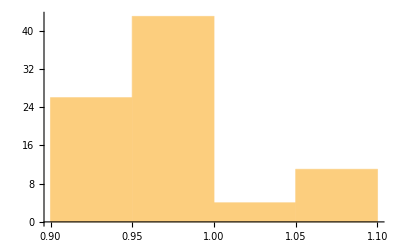

{0.932293,0.976816,1.02134}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonGhostVertex[DummyArrayK[2],μ,p1,ν,p2]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

{1887.93,Null}

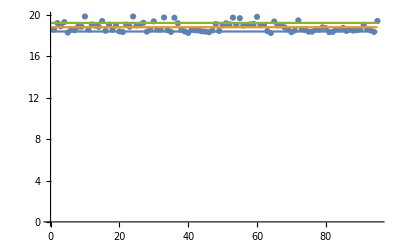

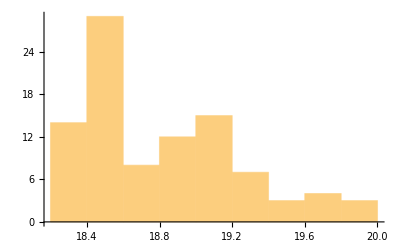

{18.4073,18.8225,19.2378}

```mathematica
theData = {};
For[i=1,i<=100,i++,
	<<GravitonVertex`;
	AppendTo[theData,Timing[GravitonGhostVertex[DummyArrayK[3],μ,p1,ν,p2]][[1]]];
	Clear[GravitonVertex`GravitonVertex];
]//Timing
theData=Nest[DeleteAnomalies,theData,3];
Show[{ListPlot[theData,AxesOrigin->{0,0}],Plot[{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]},{x,0,Length[theData]}]}]
Histogram[theData]
{Mean[theData]-StandardDeviation[theData],Mean[theData],Mean[theData]+StandardDeviation[theData]}
```

```mathematica
NotebookSave[];
```